```mathematica
Ejercicio 1. Estudiar si los siguientes grafos son regulares,completos,bipartitos y/o bipartitos completos:
a) G1 el grafo de la práctica anterior
```

```mathematica
W1={1,2,3,4,5,6,7,8}
F1={2->5,2->8,1->4,1->6,1->7,3->4,3->6,3->7}
```

{1,2,3,4,5,6,7,8}

{2→5,2→8,1→4,1→6,1→7,3→4,3→6,3→7}

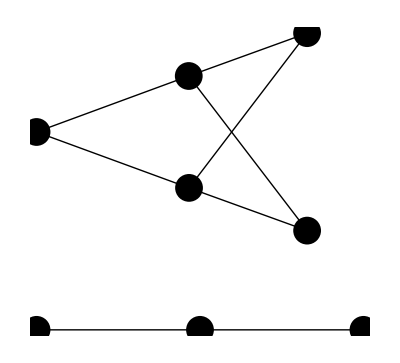

```mathematica
GraphPlot[F1,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
G1=Graph[{{{2,5}},{{2,8}},{{1,4}} ,{{1,6}} ,{{1,7}} ,{{3,4}} ,{{3,6}} ,{{3,7}}},  {{{-1,2}},{{-2,1}},{{-2,-1}} ,{{-1,-2}} ,{{1,-2}} ,{{-1,-2}} ,{{2,1}} ,{{1,2}}}]
```

Graph[{{{2,5}},{{2,8}},{{1,4}},{{1,6}},{{1,7}},{{3,4}},{{3,6}},{{3,7}}},{{{-1,2}},{{-2,1}},{{-2,-1}},{{-1,-2}},{{1,-2}},{{-1,-2}},{{2,1}},{{1,2}}}]

```mathematica
GRADO[n_,F_]:=Module[{i},
grado=0;
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},{n}]=={n},grado++],{i,Length[F]}];
grado
]
```

```mathematica
Sum[GRADO[i,F],{i,Length[W]}]==Length[F]*2
```

True

```mathematica
REGULAR2[W_,F_]:=Module[{i,j},
grado=GRADO[W[[1]],F];
regular=True;
Do[
If[grado≠GRADO[W[[i]],F],regular=False];
,{i,2,Length[W]}];
If[regular,Print["El grafo es ",grado,"-regular"],Print["El grafo no es regular"];]
];
```

```mathematica
REGULAR2[W1,F1]
```

El grafo no es regular

```mathematica
MATRIZADYACENCIADIR[W_,F_]:=Module[{i,CONTADORi,nuevoF},         
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=SparseArray[Table[{nuevoF[[i]][[1]],nuevoF[[i]][[2]]}->1,{i,Length[F]}],{Length[W],Length[W]}];
Normal[matrizadyacencia]
];
```

```mathematica
A1=MATRIZADYACENCIADIR[W1,F1];
MatrixForm[A1]
```

(0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
COMPLETO[matrizadyacencia_]:=   (Sum[MatrixPower[matrizadyacencia,2][[i,i]],{i,Dimensions[matrizadyacencia][[1]]}]==Dimensions[matrizadyacencia][[1]]*(Dimensions[matrizadyacencia][[1]]-1))
```

```mathematica
COMPLETO[A1]
```

False

```mathematica
<<"Combinatorica`";
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
IND[W1_,F_]:=Module[{i},
F1={};
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},W1]=={F[[i]][[1]],F[[i]][[2]]},AppendTo[F1,F[[i]]]],{i,Length[F]}];
F1
]
```

```mathematica
BIPARTITO[W_,F_]:=Module[{i,subconjuntos,j,fin},
bipartito=False;
i=1;
fin=Quotient[Length[W],2];
While[!bipartito && i<=fin,
subconjuntos=KSubsets[W,i];
j=1;
While[!bipartito && j<=Length[subconjuntos],
If[IND[subconjuntos[[j]],F]=={},
If[IND[Complement[W,subconjuntos[[j]]],F]=={},
bipartito=True;
W1=subconjuntos[[j]];
W2=Complement[W,subconjuntos[[j]]];
];
];
j++;];
i++;];
If[bipartito,Print["Es bipartito: W1=",W1," y W2=",W2];
If[Length[F]==Length[W1]*Length[W2],Print["Es bipartito completo: ",Subscript["K", Length[W1],Length[W2]]  ], Print["No es bipartito completo"]];
,Print["No es bipartito"]];
]
```

```mathematica
BIPARTITO[W1,F1]
```

Es bipartito: W1={1,2,3} y W2={4,5,6,7,8}

No es bipartito completo

```mathematica
b) Un hexágono
```

```mathematica
W2={1,2,3,4,5,6}
F2={1->2,2->3,3->4,4->5,5->6,6->1}
```

{1,2,3,4,5,6}

{1→2,2→3,3→4,4→5,5→6,6→1}

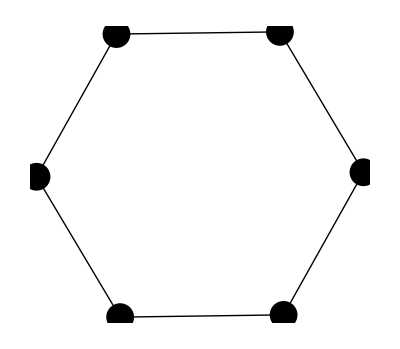

```mathematica
GraphPlot[F2,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
G1=Graph[{{{1,2}},{{2,3}},{{3,4}} ,{{4,5}} ,{{5,6}} ,{{6,1}}},  {{{-1,2}},{{-2,0}},{{-1,-2}} ,{{1,-2}} ,{{2,0}} ,{{1,2}}}]
```

⁃Graph:<6,6,Undirected>⁃

```mathematica
GRADO[n_,F_]:=Module[{i},
grado=0;
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},{n}]=={n},grado++],{i,Length[F]}];
grado
]
```

```mathematica
Sum[GRADO[i,F],{i,Length[W]}]==Length[F]*2
```

True

```mathematica
REGULAR2[W_,F_]:=Module[{i,j},
grado=GRADO[W[[1]],F];
regular=True;
Do[
If[grado≠GRADO[W[[i]],F],regular=False];
,{i,2,Length[W]}];
If[regular,Print["El grafo es ",grado,"-regular"],Print["El grafo no es regular"];]
];
```

```mathematica
REGULAR2[W1,F1]
```

El grafo es 0-regular

```mathematica
MATRIZADYACENCIADIR[W_,F_]:=Module[{i,CONTADORi,nuevoF},         
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=SparseArray[Table[{nuevoF[[i]][[1]],nuevoF[[i]][[2]]}->1,{i,Length[F]}],{Length[W],Length[W]}];
Normal[matrizadyacencia]
];
```

```mathematica
A2=MATRIZADYACENCIADIR[W2,F2];
MatrixForm[A2]
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
COMPLETO[A2]
```

False

```mathematica
BIPARTITO[W2,F2]
```

Es bipartito: W1={1,3,5} y W2={2,4,6}

No es bipartito completo

```mathematica
c) K6
```

```mathematica
W3={1,2,3,4,5,6}
F3={1->2,1-> 3,1->4,1->5,1->6,2->3,2->4,2->5,2->6,3->4,3->5,3->6,4->5,4->6,5->6}
A3={{0,1,1,1,1,1},{1,0,1,1,1,1},{1,1,0,1,1,1},{1,1,1,0,1,1},{1,1,1,1,0,1},{1,1,1,1,1,0}};
```

{1,2,3,4,5,6}

{1→2,1→3,1→4,1→5,1→6,2→3,2→4,2→5,2→6,3→4,3→5,3→6,4→5,4→6,5→6}

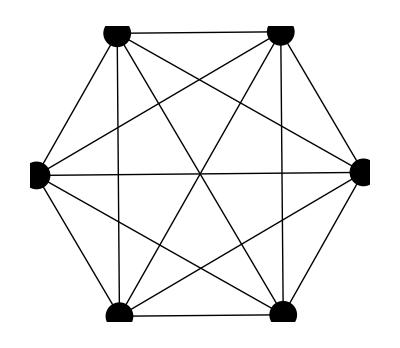

```mathematica
GraphPlot[F3,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
REGULAR2[W3,F3]
```

El grafo es 5-regular

```mathematica
MatrixForm[A3]
```

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 0)

```mathematica
COMPLETO[A3]
```

True

```mathematica
BIPARTITO[W3,F3]
```

No es bipartito

```mathematica
d) K2,3
```

```mathematica
W4={1,2,3,4,5}
F4={1-> 3,1->4,1->5, 2->3,2->4,2->5}
```

{1,2,3,4,5}

{1→3,1→4,1→5,2→3,2→4,2→5}

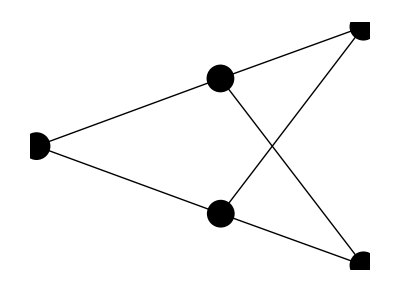

```mathematica
GraphPlot[F4,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
REGULAR2[W4,F4]
```

El grafo no es regular

```mathematica
A4=MATRIZADYACENCIADIR[W4,F4];
MatrixForm[A4]
```

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
COMPLETO[A4]
```

False

```mathematica
BIPARTITO[W4,F4]
```

Es bipartito: W1={1,2} y W2={3,4,5}

Es bipartito completo: K_(2,3)

```mathematica
e) Sea V el conjunto formado por los primeros 8 elementos del conjunto formado por todas
las cifras distintas que componen su DNI y todas las letras distintas de su primer
apellido.Consideramos el grafo no orientado G cuyo conjunto de vértices es V y dos vértices
cualesquiera serán adyacentes si y sólo si son:Un número par y un número impar.Una vocal y un número par.Una consonante y una vocal.
```

```mathematica
W5={7,3,6,5,8,4,3,a,b};
F5={7->6,7-> 4,7-> 8, 3-> 6, 3-> 8, 3->4, 6-> 5, 6-> a, 5->4,5->8,8->4,a->b}
```

{7→6,7→4,7→8,3→6,3→8,3→4,6→5,6→a,5→4,5→8,8→4,a→b}

```mathematica
indiceV[W_,F_]:=Module[{CONTADORi,nuevoF},nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];,{CONTADORi,Length[F]}];
nuevoF]
```

```mathematica
W6=Table[i,{i,Length[W5]}];
F6=indiceV[W5,F5];
```

```mathematica
W6
F6
```

{1,2,3,4,5,6,7,8,9}

{1→3,1→6,1→5,2→3,2→5,2→6,3→4,3→8,4→6,4→5,5→6,8→9}

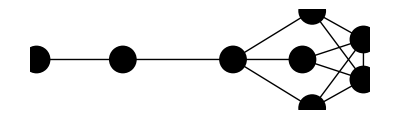

```mathematica
GraphPlot[F6,PlotStyle->{Black,PointSize[.05]}]
```

```mathematica
REGULAR2[W6,F6]
```

El grafo no es regular

```mathematica
A6=MATRIZADYACENCIADIR[W6,F6];
MatrixForm[A6]
```

(0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
COMPLETO[A6]
```

False

```mathematica
BIPARTITO[W6,F6]
```

No es bipartito